```mathematica
legendoptions={LabelStyle->{Bold,GrayLevel[0.3],14},LegendMarkerSize->{15,10}};
```

#### Círculo

Circulo do porta-amostras

```mathematica
r :=1.27*4

upcircle[x_] := Sqrt[r^2-x^2]
lowcircle[x_] := -Sqrt[r^2-x^2]
gcircleup := Plot[upcircle[x],{x,-r,r},PlotStyle->{Black},PlotLegends->Placed[LineLegend[{"Porta-Alvos"},legendoptions],Above]]
gcirclelow := Plot[lowcircle[x],{x,-r,r},PlotStyle->{Black}]
```

Circulo da pos 2

```mathematica
r2 := 2.54
upcircle2[x_] := Sqrt[r2^2-x^2]
lowcircle2[x_] := -Sqrt[r2^2-x^2]
gcircleup2 := Plot[upcircle2[x],{x,-r2,r2},PlotStyle->{Orange,Dashed,Thick},PlotLegends->Placed[LineLegend[{"r = 2.54cm"},legendoptions],Above]]
gcirclelow2 := Plot[lowcircle2[x],{x,-r2,r2},PlotStyle->{Orange,Dashed,Thick}]
```

Circulo da pos 3

```mathematica
r3:= 3.81
upcircle3[x_] := Sqrt[r3^2-x^2]
lowcircle3[x_] := -Sqrt[r3^2-x^2]
gcircleup3 := Plot[upcircle3[x],{x,-r3,r3},PlotStyle->{Brown,Dashed,Thick},PlotLegends->Placed[LineLegend[{"r = 3.81cm"},legendoptions],Above]]
gcirclelow3 := Plot[lowcircle3[x],{x,-r3,r3},PlotStyle->{Brown,Dashed,Thick}]
```

#### Ângulos

```mathematica
a1u := 10.8*Pi/180
a1l := -9.4*Pi/180
a1ureta[x_] :=Tan[a1u]*x 
intersecta1u := Solve[a1ureta[x] == Sqrt[r2^2-x^2],x]
xia1u := First[x/.intersecta1u]
ga1u:=Plot[a1ureta[u],{u,0,xia1u},PlotStyle->{Orange}]



a1lreta[x_] :=Tan[a1l]*x 
intersecta1l := Solve[a1lreta[x] == -Sqrt[r2^2-x^2],x]
xia1l := First[x/.intersecta1l]
ga1l:=Plot[a1lreta[u],{u,0,xia1l},PlotStyle->{Orange}]







a2u := 36.7*Pi/180
a2l := -38.9*Pi/180
a2ureta[x_] :=Tan[a2u]*x 
intersecta2u := Solve[a2ureta[x] == Sqrt[r3^2-x^2],x]
xia2u := First[x/.intersecta2u]
ga2u:=Plot[a2ureta[u],{u,0,xia2u},PlotStyle->{Brown}]



a2lreta[x_] :=Tan[a2l]*x 
intersecta2l := Solve[a2lreta[x] == -Sqrt[r3^2-x^2],x]
xia2l := First[x/.intersecta2l]
ga2l:=Plot[a2lreta[u],{u,0,xia2l},PlotStyle->{Brown}]


















a3u := 170.6*Pi/180
a3l := 192.8*Pi/180
a3ureta[x_] :=Tan[a3u]*x 
intersecta3u := Solve[a3ureta[x] == Sqrt[r2^2-x^2],x]
xia3u := First[x/.intersecta3u]
ga3u:=Plot[a3ureta[u],{u,0,xia3u},PlotStyle->{Orange}]



a3lreta[x_] :=Tan[a3l]*x 
intersecta3l := Solve[a3lreta[x] == -Sqrt[r2^2-x^2],x]
xia3l := First[x/.intersecta3l]
ga3l:=Plot[a3lreta[u],{u,0,xia3l},PlotStyle->{Orange}]







a4u := 141.7*Pi/180
a4l := 218.5*Pi/180
a4ureta[x_] :=Tan[a4u]*x 
intersecta4u := Solve[a4ureta[x] == Sqrt[r3^2-x^2],x]
xia4u := First[x/.intersecta4u]
ga4u:=Plot[a4ureta[u],{u,0,xia4u},PlotStyle->{Brown}]



a4lreta[x_] :=Tan[a4l]*x 
intersecta4l := Solve[a4lreta[x] == -Sqrt[r3^2-x^2],x]
xia4l := First[x/.intersecta4l]
ga4l:=Plot[a4lreta[u],{u,0,xia4l},PlotStyle->{Brown}]
```

#### Retas que delimitam a área não detectável

```mathematica
m:=3.21748
b :=-7.5517 

reta1[x_] :=m*x+b
intersectr1 := Solve[reta1[x] == Sqrt[r^2-x^2],x]
xr1 := First[x/.intersectr1]





m2:=-4.3067
b2 :=10.3773 

reta2[x_] :=m2*x+b2
intersectr2 := Solve[reta2[x] == -Sqrt[r^2-x^2],x]
xr2 := First[x/.intersectr2]
intersectreta := Solve[reta1[x] == reta2[x],x]
xretas := First[x/.intersectreta]
g1:=Plot[reta1[u],{u,xretas,xr1},PlotStyle->{Red}]
g2:=Plot[reta2[u],{u,xretas,xr2},PlotStyle->{Red}]




m3:=-4.02085
b3 :=-9.66096 

reta3[x_] :=m3*x+b3
intersectr3 := Solve[reta3[x] == Sqrt[r^2-x^2],x]
xr3 := First[x/.intersectr3]






m4:=3.58328
b4:=8.31262 

reta4[x_] :=m4*x+b4
intersectr4 := Solve[reta4[x] == -Sqrt[r^2-x^2],x]
xr4 := First[x/.intersectr4]
intersectreta2 := Solve[reta3[x] == reta4[x],x]
xretas2 := First[x/.intersectreta2]
g3:=Plot[reta3[u],{u,xr3,xretas2},PlotStyle->{Red}]
g4:=Plot[reta4[u],{u,xr4,xretas2},PlotStyle->{Red}]
```

#### Desenhar a vermelho as fronteiras do circulo do porta/amostras n\ao detectaveis

```mathematica
upcircledet[x_] := Sqrt[r^2-x^2]
lowcircledet[x_] := -Sqrt[r^2-x^2]
gcircleupdet := Plot[upcircledet[x],{x,xr1,r},PlotStyle->{Red}]
gcirclelowdet := Plot[lowcircledet[x],{x,xr2,r},PlotStyle->{Red}]
gcircleupdet2 := Plot[upcircledet[x],{x,-r,xr3},PlotStyle->{Red}]
gcirclelowdet2 := Plot[lowcircledet[x],{x,-r,xr4},PlotStyle->{Red}]
```

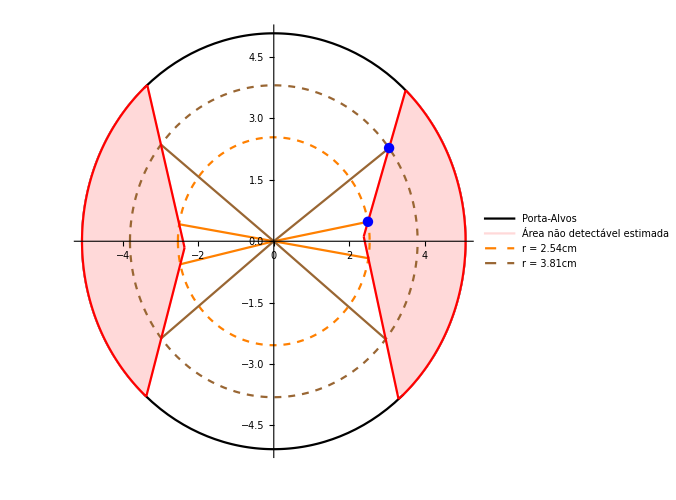

area_detetavel.pdf

```mathematica
shaded1 := RegionPlot[y<reta1[x]&& y>reta2[x] && y<upcircle[x] && y>lowcircle[x] ,{x,-r,r},{y,-r,r},BoundaryStyle->{LightRed},PlotStyle->{LightRed},PlotLegends->Placed[LineLegend[{"Área não detectável estimada"},legendoptions],Above]]

shaded2 := RegionPlot[y<reta3[x]&& y>reta4[x] && y<upcircle[x] && y>lowcircle[x] ,{x,-r,r},{y,-r,r},BoundaryStyle->{LightRed},PlotStyle->{LightRed}]

Show[gcircleup,gcirclelow,shaded1,shaded2,gcircleup2,gcirclelow2,gcircleup3,gcirclelow3,ga1u,ga1l,ga2u,ga2l,ga3u,ga3l,ga4u,ga4l,g1,g2,g3,g4,gcircleupdet,gcircleupdet2,gcirclelowdet,gcirclelowdet2,Graphics[{PointSize[0.015],Blue,Point[{xia1u,reta1[xia1u]}]}],Graphics[{PointSize[0.015],Blue,Point[{xia2u,reta1[xia2u]}]}],PlotRange->{{-r,r},{-r,r}},AspectRatio->1,ImageSize->500]


Export["area_detetavel.pdf",%]
```

```mathematica
ExpandFileName["area_detetavel.pdf"]
```

C:\Users\pcmultimedia\Documents\area_detetavel.pdf